The effect of direct electron-positron pair production on relativistic feedback rates

Authors: I. B. Vodopiyanov, J. R. Dwyer, E. S. Cramer, R. J. Lucia, and H. K. Rassoul

Link to paper: https://agupubs.onlinelibrary.wiley.com/doi/10.1002/2014JA020415

Notebook by: Óscar Amaro (2023)

## Figure 1

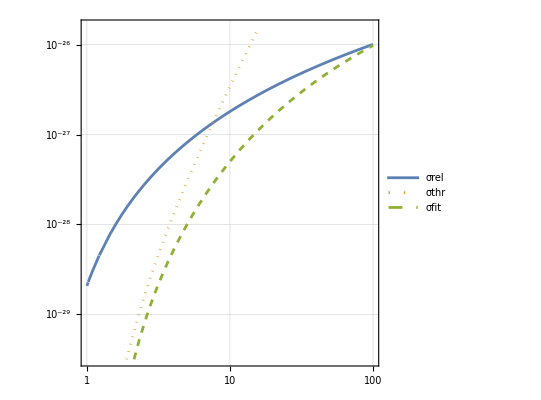

```mathematica
Clear[Z,re,α,E0,σrel,σthr,σfit,mc2]
α=1/137;(*fine structure constant*)
re=2.82 10^-15;(*[m] classical electron radius*)
Z=7;(*nitrogen*)
(* we multiply all expressions by 10^4 to convert from m^2 to cm^2. also, energy E0 or T0 is in MeV, so mc^2=0.511*)
mc2=0.511;(*[MeV]*)
σrel=(28Z^2 re^2 α^2)/(27π)Log[E0/mc2]^3 10^4;(*eq1*)
σthr=(7Z^2 re^2 α^2)/2304(E0-2mc2)^3/(mc2)^3 10^4;(*eq2*)
σfit=5.22 Z^2 Log[(2.3+E0)/3.52]^3 10^4 (10^-28 10^-6);(*eq3*)
LogLogPlot[{σrel,σthr,σfit},{E0,1,100},AspectRatio->1,GridLines->Automatic,Frame->True,PlotStyle->{Default,Dotted,Dashed},PlotRange->{10^-29.5,10^-25.8}
,PlotLegends->{"σrel","σthr","σfit"}]
```